```mathematica
Rendering Equation Plot
```

```mathematica
Clear["Global`*"];
rule1 = {ϵ -> 78*10^3 };
```

```mathematica
L[d_,c_] := NIntegrate[2*10^(-d*c*ϵ/Cos[t])*Cos[t]Sin[t],{t,0,Pi/2.3}]/.rule1
```

```mathematica
Plot3D[L[x,y],{x,0,10},{y,0,1}, PlotLabel-> Absorbance ]
```

NIntegrate::inumr: The integrand 2^(1-5.11225×10^-8 ϵ Sec[t]) 5^(-5.11225×10^-8 ϵ Sec[t]) Cos[t] Sin[t] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1.0472}}.

-Graphics3D-

```mathematica
Rasterize[%8,"Image"]
```

-Graphics-

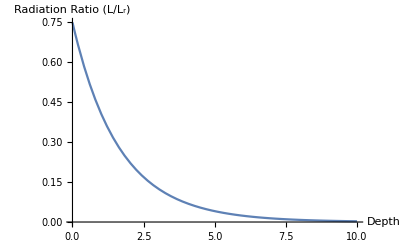

```mathematica
Plot[L[x,.2],{x,0,10},AxesLabel->{"Depth","Radiation Ratio (L/L_r)"}]
```

NIntegrate::inumr: The integrand 2^(1-4.08571×10^-6 ϵ Sec[t]) 5^(-4.08571×10^-6 ϵ Sec[t]) Cos[t] Sin[t] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1.0472}}.

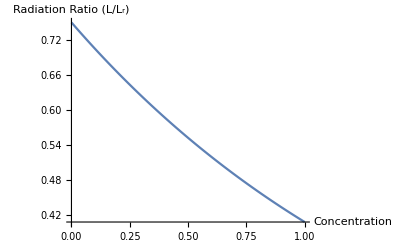

```mathematica
Plot[L[.2,x],{x,0,1},AxesLabel->{"Concentration","Radiation Ratio (L/L_r)"}]
```

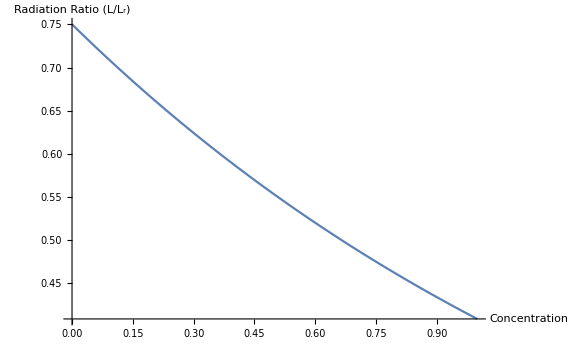

```mathematica
Show[%25,ImageSize->Large]
```

```mathematica
Show[%26,ImageSize->Large]
```

-Graphics-

```mathematica
Export["/Users/shehtabzaman/Documents/CS-Research/notes/2dPlotConcentration.jpg",%27,"JPEG"]
```

/Users/shehtabzaman/Documents/CS-Research/notes/2dPlotConcentration.jpg

```mathematica
L[50,10^-7]
```

0.232638

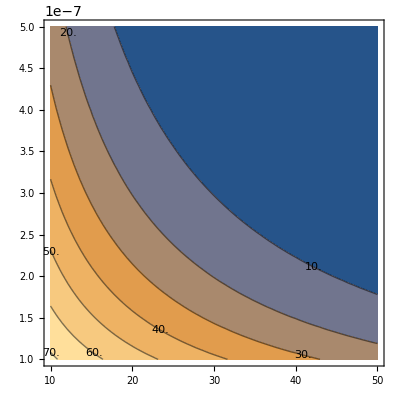

```mathematica
ContourPlot[100*L[x,y],{x,10,50},{y,10^-7,5*10^-7},ContourLabels->All]
```

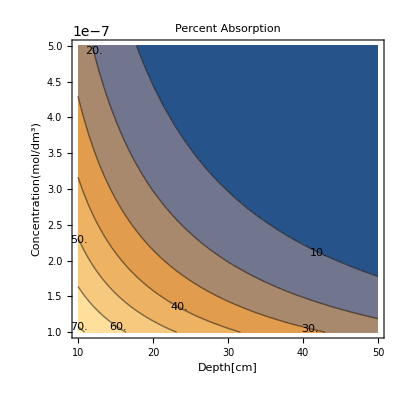

```mathematica
Show[%34,FrameLabel->{{HoldForm[Concentration[mol/dm^3]],None},{HoldForm[Depth[cm]],None}},PlotLabel->HoldForm[Percent Absorption],LabelStyle->{GrayLevel[0]}]
```

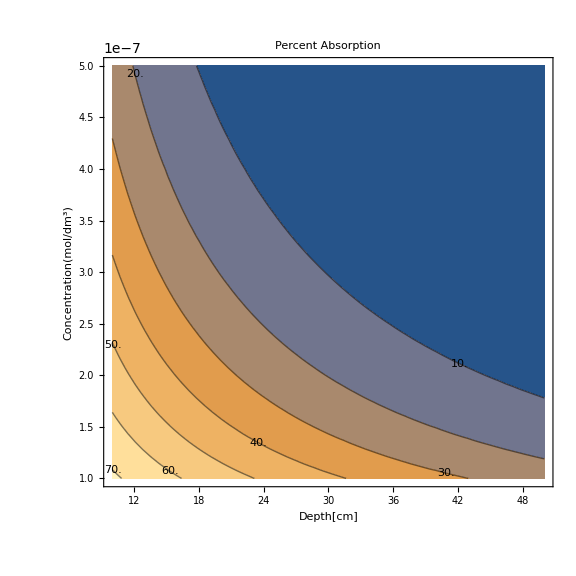

```mathematica
Show[%35,ImageSize->Large,ContourLabels->All]
```

```mathematica
Export["/Users/shehtabzaman/Documents/CS-Research/notes/ContourPlot.jpg",%36,"JPEG"]
```

/Users/shehtabzaman/Documents/CS-Research/notes/ContourPlot.jpg

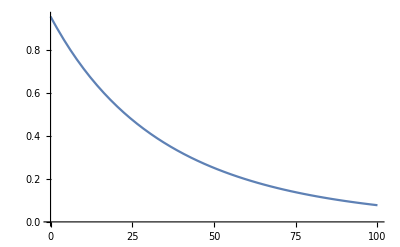

```mathematica
Plot[L[x,10^-7],{x,0,100}]
```

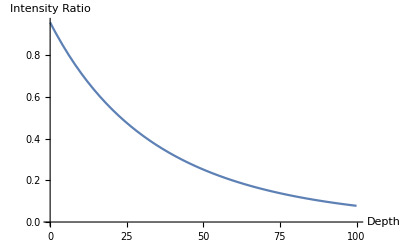

```mathematica
Show[%41,AxesLabel->{HoldForm[Depth],HoldForm[Intensity Ratio]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

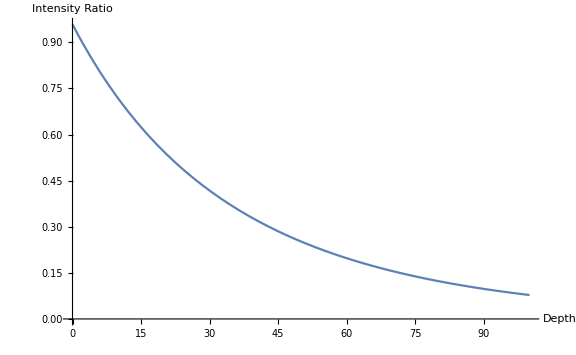

```mathematica
Show[%43,ImageSize->Large]
```

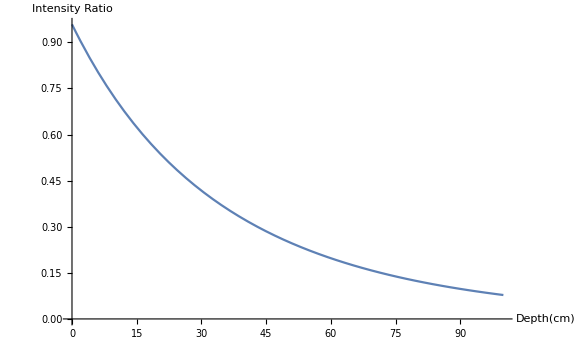

```mathematica
Show[%44,AxesLabel->{HoldForm[HoldForm[Depth][cm]],HoldForm[Intensity Ratio]},PlotLabel->None]
```

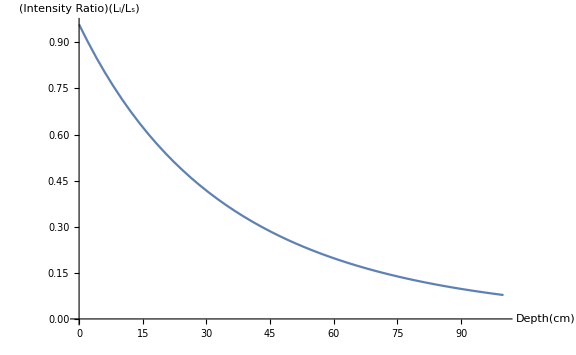

```mathematica
Show[%45,AxesLabel->{HoldForm[HoldForm[Depth][cm]],HoldForm[HoldForm[Intensity Ratio][Subscript[L, i]/Subscript[L, s]]]},PlotLabel->None]
```

```mathematica
Export["/Users/shehtabzaman/Documents/CS-Research/notes/2dPlot.jpg",%46,"JPEG"]
```

/Users/shehtabzaman/Documents/CS-Research/notes/2dPlot.jpg

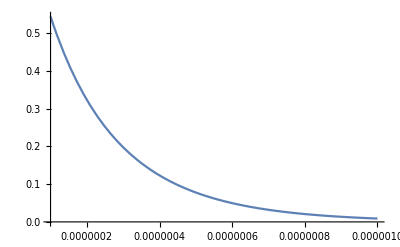

```mathematica
Plot[L[20,y],{y,10^-7,10^-6}]
```

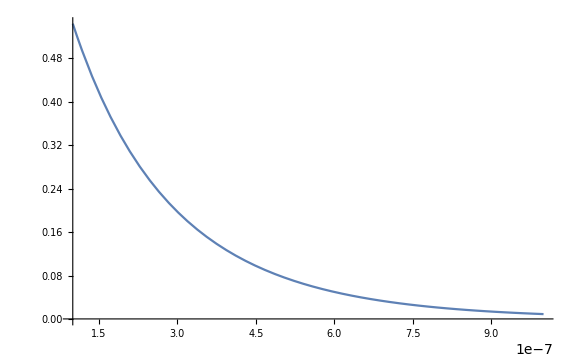

```mathematica
Show[%48,ImageSize->Large]
```

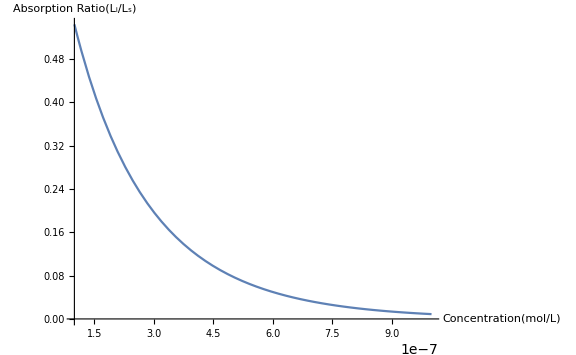

```mathematica
Show[%49,AxesLabel->{HoldForm[Concentration[mol/L]],HoldForm[Absorption Ratio[Subscript[L, i]/Subscript[L, s]]]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["/Users/shehtabzaman/Documents/CS-Research/notes/2dPlotConcentration.jpg",%50,"JPEG"]
```

/Users/shehtabzaman/Documents/CS-Research/notes/2dPlotConcentration.jpg